```mathematica
PartData2[p_]:=Block[{n=Total[p],total,removed,edges,mpg,toomany},
total=n(n-1)/2;
removed=Total[Map[#(#-1)/2&,p]];
edges = total-removed;
mpg=3n-6;
toomany=edges-mpg;
{n,p,total, removed, edges,mpg, toomany}
]
```

```mathematica
TableForm[
Sort[
Flatten[
Table[
Map[
PartData2
,
DeleteDuplicates[
Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[JacobsThalGraph[k]]]]
]
,{k,1,12}],
1]
],
TableDepth->2,TableHeadings->{None, {"n","partition","total possible edges","removed", "edges", "mpg edges", "too many"}}]
```

n | partition | total possible edges | removed | edges | mpg edges | too many
5 | {2,1,1,1} | 10 | 1 | 9 | 9 | 0
6 | {2,2,1,1} | 15 | 2 | 13 | 12 | 1
7 | {2,2,2,1} | 21 | 3 | 18 | 15 | 3
8 | {2,2,2,2} | 28 | 4 | 24 | 18 | 6
8 | {3,2,2,1} | 28 | 5 | 23 | 18 | 5
8 | {3,3,1,1} | 28 | 6 | 22 | 18 | 4
9 | {3,2,2,2} | 36 | 6 | 30 | 21 | 9
9 | {3,3,2,1} | 36 | 7 | 29 | 21 | 8
10 | {3,3,2,2} | 45 | 8 | 37 | 24 | 13
10 | {4,2,2,2} | 45 | 9 | 36 | 24 | 12
10 | {4,3,2,1} | 45 | 10 | 35 | 24 | 11
10 | {4,4,1,1} | 45 | 12 | 33 | 24 | 9
11 | {3,3,3,2} | 55 | 10 | 45 | 27 | 18
11 | {4,3,2,2} | 55 | 11 | 44 | 27 | 17
11 | {4,4,2,1} | 55 | 13 | 42 | 27 | 15
12 | {4,3,3,2} | 66 | 13 | 53 | 30 | 23
12 | {4,4,2,2} | 66 | 14 | 52 | 30 | 22
12 | {5,3,2,2} | 66 | 15 | 51 | 30 | 21
12 | {5,4,2,1} | 66 | 17 | 49 | 30 | 19
12 | {5,5,1,1} | 66 | 20 | 46 | 30 | 16
13 | {4,4,3,2} | 78 | 16 | 62 | 33 | 29
13 | {5,3,3,2} | 78 | 17 | 61 | 33 | 28
13 | {5,4,2,2} | 78 | 18 | 60 | 33 | 27
13 | {5,5,2,1} | 78 | 21 | 57 | 33 | 24
14 | {4,4,4,2} | 91 | 19 | 72 | 36 | 36
14 | {5,4,3,2} | 91 | 20 | 71 | 36 | 35
14 | {5,5,2,2} | 91 | 22 | 69 | 36 | 33
14 | {6,3,3,2} | 91 | 22 | 69 | 36 | 33
14 | {6,4,2,2} | 91 | 23 | 68 | 36 | 32
14 | {6,5,2,1} | 91 | 26 | 65 | 36 | 29
14 | {6,6,1,1} | 91 | 30 | 61 | 36 | 25
15 | {5,4,4,2} | 105 | 23 | 82 | 39 | 43
15 | {5,5,3,2} | 105 | 24 | 81 | 39 | 42
15 | {6,4,3,2} | 105 | 25 | 80 | 39 | 41
15 | {6,5,2,2} | 105 | 27 | 78 | 39 | 39
15 | {6,6,2,1} | 105 | 31 | 74 | 39 | 35
16 | {5,5,4,2} | 120 | 27 | 93 | 42 | 51
16 | {6,4,4,2} | 120 | 28 | 92 | 42 | 50
16 | {6,5,3,2} | 120 | 29 | 91 | 42 | 49
16 | {6,6,2,2} | 120 | 32 | 88 | 42 | 46
16 | {7,4,3,2} | 120 | 31 | 89 | 42 | 47
16 | {7,5,2,2} | 120 | 33 | 87 | 42 | 45
16 | {7,6,2,1} | 120 | 37 | 83 | 42 | 41
16 | {7,7,1,1} | 120 | 42 | 78 | 42 | 36

```mathematica
TableForm[
Sort[
Flatten[
Table[
Map[
PartData2
,
DeleteDuplicates[
Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[MinimalGraph[k]]]]
]
,{k,1,12}],
1]
],
TableDepth->2,TableHeadings->{None, {"n","partition","total possible edges","removed", "edges", "mpg edges", "too many"}}]
```

n | partition | total possible edges | removed | edges | mpg edges | too many
4 | {1,1,1,1} | 6 | 0 | 6 | 6 | 0
5 | {2,1,1,1} | 10 | 1 | 9 | 9 | 0
6 | {2,2,1,1} | 15 | 2 | 13 | 12 | 1
7 | {3,2,1,1} | 21 | 4 | 17 | 15 | 2
8 | {3,3,1,1} | 28 | 6 | 22 | 18 | 4
9 | {4,3,1,1} | 36 | 9 | 27 | 21 | 6
10 | {4,4,1,1} | 45 | 12 | 33 | 24 | 9
11 | {5,4,1,1} | 55 | 16 | 39 | 27 | 12
12 | {5,5,1,1} | 66 | 20 | 46 | 30 | 16
13 | {6,5,1,1} | 78 | 25 | 53 | 33 | 20

```mathematica
Monitor[Table[With[{g=ReadGrof[k]},{VertexCount[g],Length[DeleteDuplicates[
Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[g]]]]}],{k,20}],k]
```

{{4,1},{5,1},{6,1},{6,1},{7,1},{7,1},{7,1},{7,1},{7,1},{8,1},{8,2},{8,1},{8,1},{8,2},{8,2},{8,1},{8,1},{8,1},{8,1},{8,2}}

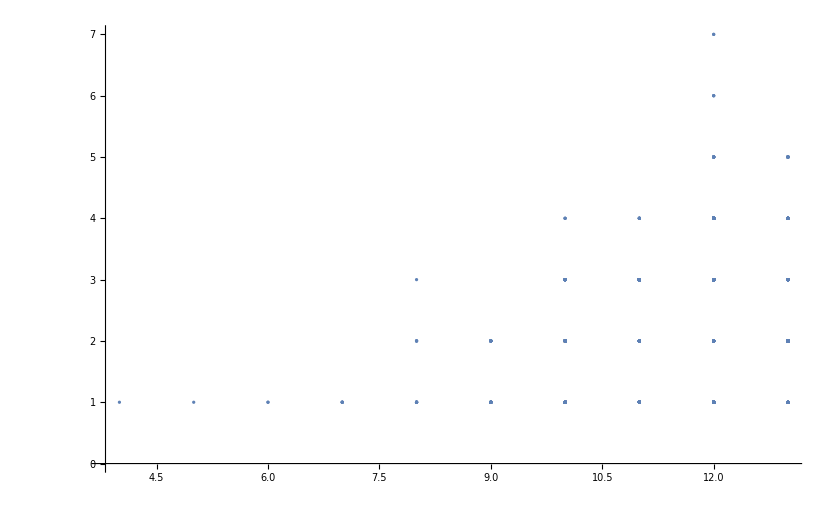

```mathematica
ListPlot[Monitor[Table[With[{g=ReadGrof[k]},{VertexCount[g],Length[DeleteDuplicates[
Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[g]]]]}],{k,10000}],k],PlotRange->All]
```

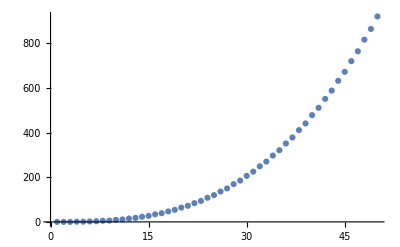

```mathematica
ListPlot[Monitor[Table[{k,Length[IntegerPartitions[k,{4}]]},{k,50}],k],PlotRange->All]
```